理解自然语言

我们之前已经看到如何使用ctrl= 来输入自然语言。现在我们要谈的是如何设置理解自然语言的函数。

Interpreter 是实现这些的关键。你告诉 Interpreter 你想得到什么类型的东西，它将接受你提供的任何字符串，并尝试以这种方式解释它。

将字符串“nyc”解释为一个城市：

```mathematica
Interpreter["City"]["nyc"]
```

New York City

“The big apple”是纽约市的一个绰号：

```mathematica
Interpreter["City"]["the big apple"]
```

New York City

将字符串 "hot pink" 解释为一种颜色：

```mathematica
Interpreter["Color"]["hot pink"]
```

RGBColor[1., 0.4117647058823529, 0.7058823529411764]

Interpreter 将自然语言转换为你可以进行计算的 Wolfram 语言表达式。这里有一个涉及货币数额的例子。

解释各种货币数额：

```mathematica
Interpreter["CurrencyAmount"][{"4.25 dollars","34 russian rubles","5 euros","85 cents"}]
```

{4.25 $,34  руб,5 €,85 ¢}

按当前汇率进行换算后计算总额：

```mathematica
Total[{Quantity[4.25, "USDollars"],Quantity[34, "RussianRubles"],Quantity[5, "Euros"],Quantity[85, "USCents"]}]
```

11.07 $

这里有另一个例子，涉及到地点。

Interpreter 将给出白宫的地理位置：

```mathematica
Interpreter["Location"]["White House"]
```

GeoPosition[{38.8977,-77.0366}]

它也适用于街道地址：

```mathematica
Interpreter["Location"]["1600 Pennsylvania Avenue, Washington, DC"]
```

GeoPosition[{38.8977,-77.0366}]

Interpreter 可以处理数百种不同类型的对象：

解释大学的名称：
Interpret names of universities (which “U of I” is picked depends on geo location):

```mathematica
Interpreter["University"][{"Harvard","Stanford","U of I"}]
```

{Harvard University,Stanford University,University of Illinois at Urbana-Champaign}

解释化学名称：

```mathematica
Interpreter["Chemical"][{"H2O","aspirin","CO2","wolfram"}]
```

{water,aspirin,carbon dioxide,tungsten}

解释动物的名字，然后获取它们的图像：

```mathematica
EntityValue[Interpreter["Animal"][{"cheetah","tiger","elephant"}],"Image"]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

Interpreter 解释的是整个字符串。而 TextCases 试图从一个字符串中挑选出你所要求的实例。

在一段文本中取出名词：

```mathematica
TextCases["A sentence is a linguistic construct","Noun"]
```

{sentence,construct}

取出货币数额：

```mathematica
TextCases["Choose between $5, €5 and ¥5000","CurrencyAmount"]
```

{$5,€5,¥5000}

你可以使用 TextCases 从一段文本中挑出特定种类的东西。在这个例子中，我们在维基百科的文章中挑选出国家名称的实例。

从维基百科上关于欧盟的文章中生成一个国家名称的词云：

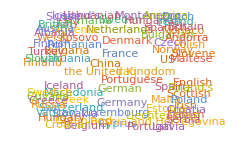

```mathematica
WordCloud[TextCases[WikipediaData["EU"],"Country"]]
```

TextStructure 将向你显示一段文本的整体结构。

找出一个英语句子如何被解析为语法单位：

```mathematica
TextStructure["You can do so much with the Wolfram Language."]
```

You
Pronoun
Noun Phrase  can
Verb  do
Verb  so
Adverbmuch
Adverb
Adverb Phrase  with
Preposition  the
DeterminerWolfram
Proper NounLanguage
Proper Noun
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase.
Punctuation
Sentence

另一种表示方法，是以图的形式：

```mathematica
TextStructure["You can do so much with the Wolfram Language.","ConstituentGraphs"]
```

{-Graphics-}

WordList[ ] 将给出一个常用单词的列表。WordList["Noun"] 等将给出指定类型的单词列表。

给出英语中常见动词列表中的前 20 个：

```mathematica
Take[WordList["Verb"],20]
```

{aah,abandon,abase,abash,abate,abbreviate,abdicate,abduct,abet,abhor,abide,abjure,ablate,abnegate,abolish,abominate,abort,abound,abrade,abridge}

研究单词的属性很容易。下面是比较常用词表中名词、动词和形容词的长度分布的直方图。

创建常用名词、动词和形容词的长度分布直方图：

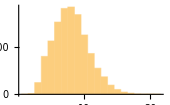
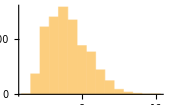
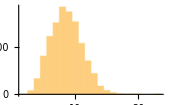

```mathematica
Histogram[StringLength[WordList[#]]]&/@{"Noun","Verb","Adjective"}
```

到目前为止，我们只谈到了英语。但 Wolfram 语言也掌握了其他语言。例如，WordTranslation 将给出单词的翻译。

将“hello”翻译为法语：

```mathematica
WordTranslation["hello","French"]
```

{bonjour,hello,holà,ohé}

翻译为韩语：

```mathematica
WordTranslation["hello","Korean"]
```

{여보세요,안녕하세요}

翻译为韩语，然后再音译成英文字母：

```mathematica
Transliterate[WordTranslation["hello","Korean"]]
```

{yeoboseyo,annyeonghaseyo}

如果你想比较很多不同的语言，请将 All 作为 WordTranslation 的语言。其结果是包含不同语言翻译的关联，这些语言大致按全球使用量的降序列出。

给出“hello”在世界上最常见的 5 种语言的翻译：

```mathematica
Take[WordTranslation["hello",All],5]
```

<|Mandarin→{表示問候的叫聲},Hindi→{हलो,नमस्ते},Spanish→{buenos días,hola},Russian→{привет,приветствие,Здравствуйте},Indonesian→{halo}|>

让我们取出前 100 种语言，并看看“hello”的第一个翻译中出现的第一个字符。这里有一个词云，显示在这些语言中，“h”是“hello”一词的翻译中最常见的起始字母。

对于前 100 种语言，将“hello”这个词的翻译的第一个字符创建为词云：

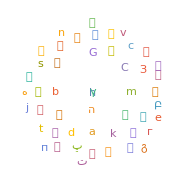

```mathematica
WordCloud[Values[StringTake[First[#],1]&/@Take[WordTranslation["hello",All],100]]]
```

词汇

Interpreter["type"] |   | 指定一个类型来解释自然语言
TextCases["text","type"] |   | 找出 text 中的所有指定类型的情况
TextStructure["text"] |   | 找出文本的语法结构
WordTranslation["word","language"] |   | 将单词翻译为其它语言

"共有 15 道习题" | "开始练习 »"

使用 Interpreter 来找出埃菲尔铁塔的位置。»

| 期望输出： |  
  | GeoPosition[{48.8583,2.29444}] |

使用 Interpreter 来找出被称为 “U of T” 的大学。»

| 期望输出： |  
  | "University of Toronto" |

使用 Interpreter 来找出被称为 C2H4、C2H6 和 C3H8 的化学物质。»

| 期望输出： |  
  | {"ethylene","ethane","propane"} |

使用 Interpreter 来解释日期 “20140108”。»

| 期望输出： |  
  | "Wed 8 Jan 2014" |

找到可以被称为 “U of X”的大学，其中 X 是字母表中的任何字母。»

| 期望输出： |  
  | {"University of Birjand","University of Chicago","The University of Edinburgh","University of Georgia","University of Houston","University of Illinois at Urbana-Champaign","University of Lethbridge","University of Michigan-Ann Arbor","University of Phoenix-Online Campus","University of Regina","University of Saskatchewan","University of Toronto"} |

查找哪些美国各州的首府名称可以被解释为电影名称(使用 CommonName 来获取实体名称的字符串版本)。»

| 期望输出： |  
  | {"Phoenix","Lincoln","Honolulu","Annapolis","Expedition: Bismarck","Providence","Nashville","Olympia","Madison"} |

找出可以用字母 a、i、l 和 m 的排列组合来指代的城市。»

| 期望输出： |  
  | {"Lima","Ilam","Milah","Mali"} |

将维基百科上关于 “火药”(gunpowder) 的文章中出现的国家名称创建为词云。»

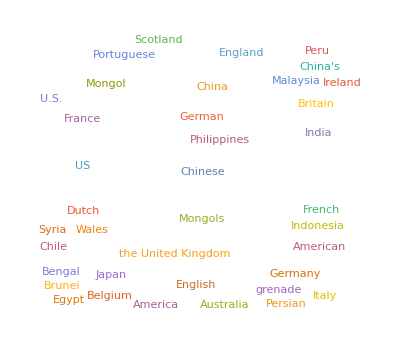
| 期望输出示例： |  
  | -Graphics- |

找出 “She sells seashells by the sea shore.” 中的所有名词。»

| 期望输出： |  
  | {"seashells","sea","shore"} |

使用 TextCases 来找出维基百科上关于计算机的文章的前 1000 个字符中的名词、动词和形容词的数量。»

| 期望输出： |  
  | {42,29,18} |

找出维基百科上关于计算机的文章中第一个句子的语法结构。»

| 期望输出示例： |  
  |  " " " ""A"
"Determiner""computer"
"Noun"
"Noun Phrase" " ""is"
"Verb" " " " ""a"
"Determiner""general-purpose"
"Adjective""device"
"Noun"
"Noun Phrase" " " " ""that"
"Determiner"
"Wh-Noun Phrase" " " " ""can"
"Verb" " ""be"
"Verb" " ""programmed"
"Verb" " " " ""to"
"Preposition" " ""carry"
"Verb" " ""out"
"Particle"
"Particle" " " " ""a"
"Determiner""set"
"Noun"
"Noun Phrase" " ""of"
"Preposition" " ""arithmetic"
"Noun""or"
"Conjunction""logical"
"Adjective""operations"
"Noun"
"Noun Phrase"
"Prepositional Phrase"
"Noun Phrase"
"Verb Phrase"
"Verb Phrase"
"Clause" " ""automatically"
"Adverb"
"Adverb Phrase"
"Verb Phrase"
"Verb Phrase"
"Verb Phrase"
"Clause"
"Clause"
"Noun Phrase"
"Verb Phrase""."
"Punctuation"
"Sentence" |

在 ExampleData[{"Text","AliceInWonderland"}] 中找出10个最常见的名词。»

| 期望输出： |  
  | {"door","voice","time","way","moment","thing","head","table","round","nothing"} |

将维基百科上关于语言的文章的第一句话的文本结构图绘制为社区图。»

| 期望输出示例： |  
  | -Graphics- |

列出在英语的 WordList 中发现的名词、动词、形容词和副词的数量。»

| 期望输出： |  
  | {25133,6671,11520,3199} |

将数字 2 到 10 的翻译为法语。»

| 期望输出： |  
  | {"deux","trois","quatre","cinq","six","sept","huit","neuf","dix"} |

问&答

解释器能解释的类型有哪些？

非常多，请查阅文档，或计算 $InterpreterTypes 以查看完整列表。

Interpreter 是否需要网络连接？

在简单的情况下，比如日期或基本货币，不需要。但对于完整的自然语言输入，是需要的。

当我说“4 dollars”时，它怎么知道我要的是美元还是其他东西？

它使用它所知道关于你的地理位置来告诉你可能想表示的货币。

Interpreter 能否处理任意的自然语言？

如果某些对象可以用 Wolfram 语言来表达，那么 Interpreter 就应该能够进行解释。Interpreter["SemanticExpression"] 能接受任何输入，并试图理解其含义，以便得到一个能够表达它的 Wolfram 语言表达式。它所做的基本上就是 Wolfram|Alpha 所做的第一阶段。

我可以添加我自己的解释器吗？

是的。GrammarRules 让你可以建立自己的语法，利用任何你想要的现有解释器。

我可以找出一个词的意思吗？

WordDefinition 将给出词典定义。

我可以找到一个词是什么类别吗？

PartOfSpeech 可以告诉你一个词可以对应的所有类别。所以对于“fish”，它给出了名词和动词。在给定的情况下，哪一个是正确的，取决于这个词在句子中是如何使用的，这就是 TextStructure 要完成的功能。

我可以翻译整个句子以及单词吗？

TextTranslation 可以对一些语言进行翻译，通常是通过调用一个外部服务来完成。

WordTranslation 能处理哪些语言？

它可以为几百种最常见的语言翻译很多词语。它至少可以翻译超过一千种语言的几个词。LanguageData 提供了超过 10,000 种语言的信息。

技术笔记

TextStructure 需要完整的语法文本，但 Interpreter 则使用了许多不同的技术，也可以处理文本片段。

当你使用ctrl= 时，你可以以交互方式解决模糊的输入。在解释器中，你必须通过程序来做，使用选项 AmbiguityFunction。

探索更多

Wolfram 中的自然语言解释器指南 »